```mathematica
p[x_]:=InterpolatingPolynomial[{{0,Sin[0]},{Pi/6,Sin[Pi/6]},{Pi/3,Sin[Pi/3]}},x]
```

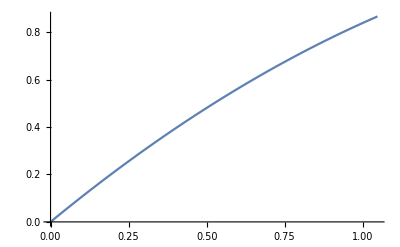

```mathematica
Plot[p[x],{x,0,Pi/3}]
```

```mathematica
Clear[f, ti, h,t]
l1[t_]=InterpolatingPolynomial[{{ti, f[ti]},{ti-h, f[ti-h]}, {ti-2h,f[ti-2h]}},t]//Simplify
```

1/(2 h^2)((2 h^2+3 h (t-ti)+(t-ti)^2) f[ti]+(t-ti) ((h+t-ti) f[-2 h+ti]-2 (2 h+t-ti) f[-h+ti]))

```mathematica
Integrate[l1[t],{t,ti,ti+h}]
```

23/12 h f[ti]+5/12 h f[-2 h+ti]-4/3 h f[-h+ti]

```mathematica
(*3-step Adams-Moulton*)Integrate[InterpolatingPolynomial[{{ti-3h,f[ti-3h]},{ti-2 h,f[ti-2 h]},{ti-h,f[ti-h]},{ti,f[ti]},{ti+h,f[ti+h]}},t]//Simplify,{t,ti,ti+h}]//Simplify
```

1/720 h (646 f[ti]-19 f[-3 h+ti]+106 f[-2 h+ti]-264 f[-h+ti]+251 f[h+ti])

```mathematica
(*4-step Adams-Bashforth*)Integrate[InterpolatingPolynomial[{{ti,f[ti]},{ti-h,f[ti-h]},{ti-2 h,f[ti-2 h]},{ti-3h,f[ti-3h]}},t]//Simplify,{t,ti,ti+h}]//Simplify
```

1/24 h (55 f[ti]-9 f[-3 h+ti]+37 f[-2 h+ti]-59 f[-h+ti])

```mathematica
du[t_, u_]:=10u(1-u);
exactSol[t_]=u[t]/.DSolve[{u'[t]==10 u[t](1-u[t]),u[0]==0.1},u[t],t][[1]];
RK4[du_,du0_, t_,T_, h_]:=Module[
{alphas,betas, p,n,y, i,k1,k2,k3,k4,tcurr,tarr},

n = Floor[(T-t)/h];

y= Table[0, n];
y[[1]]=du0;
tarr = Table[0,n];
tarr[[1]]=t;
tcurr = t+h;

For[i=2, i≤n,i++,
k1 = h*du[tcurr, y[[i-1]]]//N;
k2 = h*du[tcurr+1/2 h, y[[i-1]]+1/2 k1]//N;
k3=h*du[tcurr+1/2 h, y[[i-1]]+1/2 k2]//N;
k4 = h*du[tcurr+2/3 h,y[[i-1]]+k3]//N;
tcurr = tcurr+h;
tarr[[i]] = tcurr;
y[[i]]=y[[i-1]]+(1/6 k1+1/3 k2+1/3 k3+1/6 k4)//N; 
];

ret = Table[{tarr[[i]], y[[i]]}, {i,1,n}]
];
AB[du_,u0_,t_,T_,h_]:=Module[
{ycurr,n,len,y,i},

n =Floor[ (T-t)/h];
ycurr =RK4[du,u0,t,t+4h,h];
len = 4;

For[i = len, i≤n,i++,
y =ycurr[[i,2]]+1/24 h (
55 du[ycurr[[i,1]],ycurr[[i,2]]]
-9 du[ycurr[[i-3,1]],ycurr[[i-3,2]]]
+37 du[ycurr[[i-2,1]],ycurr[[i-2,2]]]
-59 du[ycurr[[i-1,1]],ycurr[[i-1,2]]]);

AppendTo[ycurr, {ycurr[[i,1]]+h,y }];

];
Return[ycurr];
]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

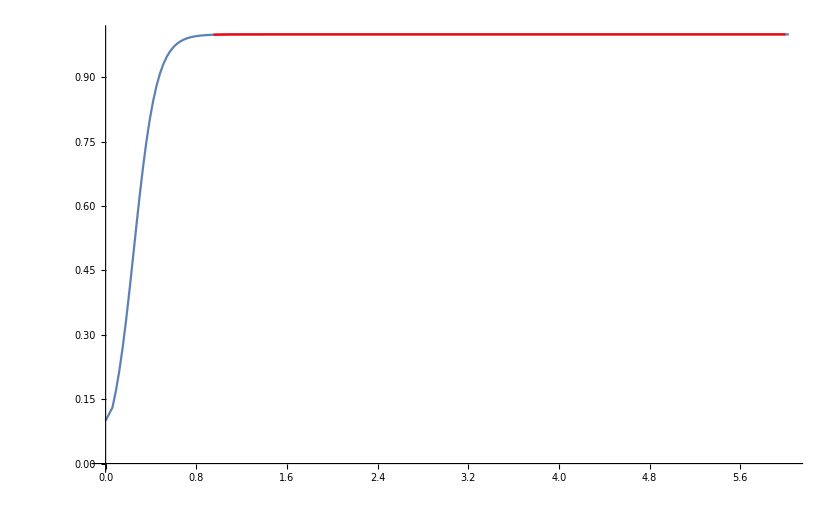

```mathematica
Show[
{ListLinePlot[AB[du,0.1,0,6,0.03],PlotRange->All],
Plot[exactSol[t],{t,0,6},PlotStyle->Red]
}]
```

ListLinePlot::prng: Value of option PlotRange -> {{0,6.1},{-1.7872052422349607542751689246531507966`15.954589770191005*^694139019579627,1.61333}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

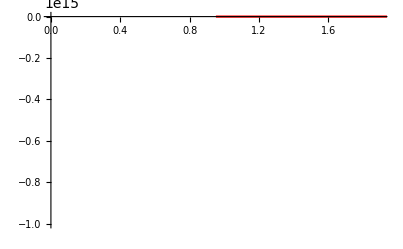
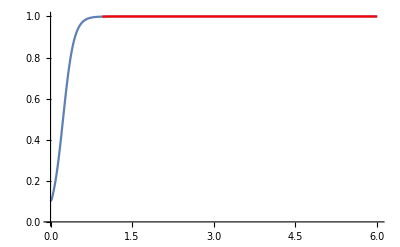
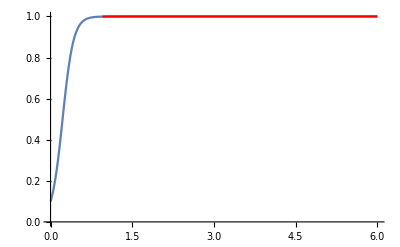

ListLinePlot::prng: Value of option PlotRange -> {{0,6.},{-0.614441,1.7872052422349607542751689246531507966`15.954589770191005*^694139019579627}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

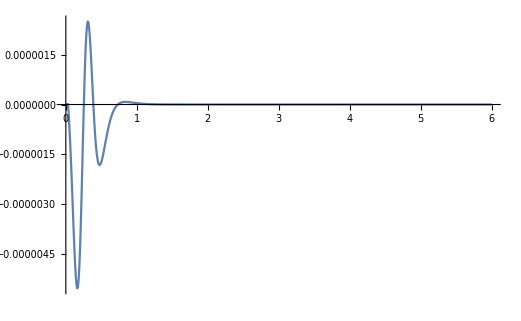
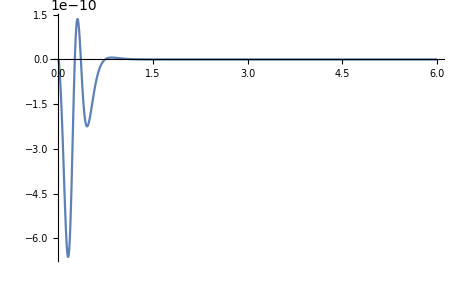
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
hh = {0.1, 0.01,0.001};
err = Table[Table[{h, exactSol[h]},{h,0,6,hh[[i]]}],{i,1,3}];
sols = Table[AB[du,0.1,0,6,hh[[i]]],{i,1,3}];
Table[
Show[
{ListLinePlot[AB[du,0.1,0,6,hh[[i]]],PlotRange->All],
Plot[exactSol[t],{t,0,6},PlotStyle->Red]
}],
{i,1,3}
]
Table[
ListLinePlot[
Table[{err[[i,p,1]],err[[i,p,2]]-sols[[i,p,2]]},
{p,1,Length[err[[i]]]}
],PlotRange->All],
{i,1,3}
]
```

```mathematica
APK[du_, u0_, t_,T_, h_, tol_]:=Module[
{ycurr,n,len,y0, y1,y2,i},

n =Floor[ (T-t)/h];
ycurr =RK4[du,u0,t,t+4h,h];
len = 4;


For[i = 4, i≤n, i++,

y0 =ycurr[[i,2]]+1/24 h (
55 du[ycurr[[i,1]],ycurr[[i,2]]]
-9 du[ycurr[[i-3,1]],ycurr[[i-3,2]]]
+37 du[ycurr[[i-2,1]],ycurr[[i-2,2]]]
-59 du[ycurr[[i-1,1]],ycurr[[i-1,2]]]);

y1 =  ycurr[[i,2]]+1/720 h(646du[ycurr[[i,1]],ycurr[[i,2]]]-19 du[ycurr[[i-3,1]],ycurr[[i-3,2]]]+106 du[ycurr[[i-2,1]],ycurr[[i-2,2]]]-264 du[ycurr[[i-1,1]],ycurr[[i-1,2]]]+251 du[ycurr[[i,1]]+h,y0]);
While[True,
y2 = ycurr[[i,2]]+1/720 h(646du[ycurr[[i,1]],ycurr[[i,2]]]-19 du[ycurr[[i-3,1]],ycurr[[i-3,2]]]+106 du[ycurr[[i-2,1]],ycurr[[i-2,2]]]-264 du[ycurr[[i-1,1]],ycurr[[i-1,2]]]+251 du[ycurr[[i,1]]+h,y1]);

If[Abs[y1-y2]<tol,
Break[],
y1=y2;
]
];
AppendTo[ycurr, {ycurr[[i,1]]+h,y2 }];

];
Return[ycurr]; 
]
```

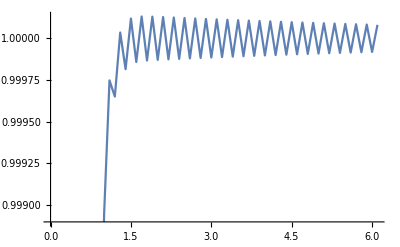

```mathematica
ListLinePlot[APK[du,0.1,0,6,0.1,0.001]]
```

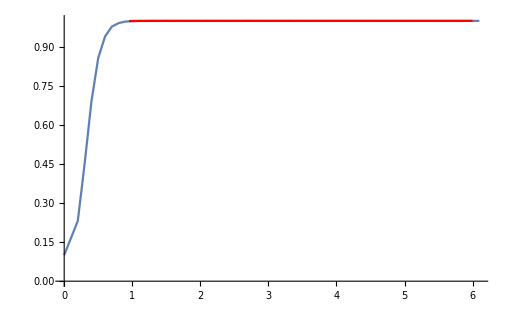
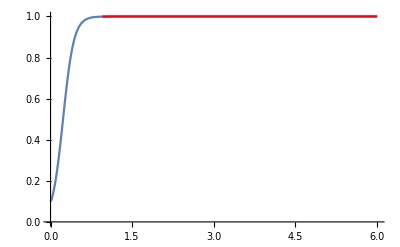
{-Graphics-,-Graphics-,-Graphics-}

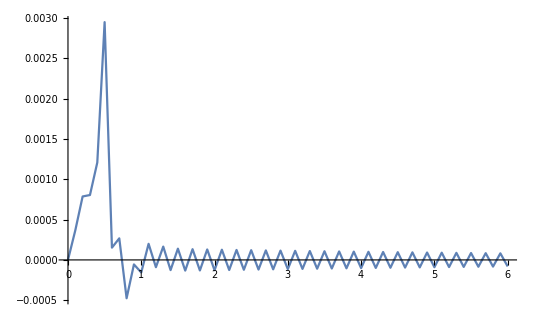
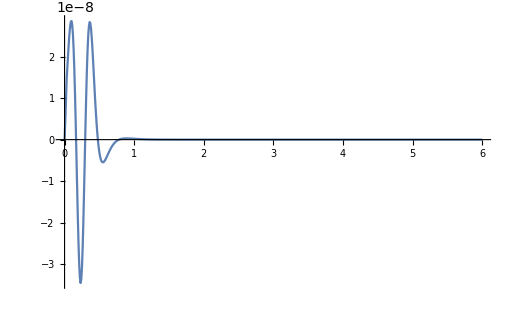
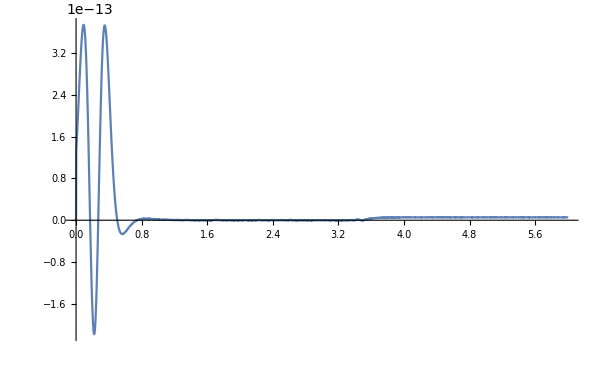

```mathematica
hh = {0.1, 0.01,0.001};
err = Table[Table[{h, exactSol[h]},{h,0,6,hh[[i]]}],{i,1,3}];
sols = Table[APK[du,0.1,0,6,hh[[i]],0.001],{i,1,3}];
Table[
Show[
{ListLinePlot[APK[du,0.1,0,6,hh[[i]],0.001],PlotRange->All],
Plot[exactSol[t],{t,0,6},PlotStyle->Red]
}],
{i,1,3}
]
Table[
ListLinePlot[
Table[{err[[i,p,1]],err[[i,p,2]]-sols[[i,p,2]]},
{p,1,Length[err[[i]]]}
],PlotRange->All],
{i,1,3}
]
```

```mathematica
y1 =fy/.FindRoot[fy == ycurr[[i,2]]+1/720 du(646du[ycurr[[i,1]],ycurr[[i,2]]]-19 du[ycurr[[i-3,1]],ycurr[[i-3,2]]]+106 du[ycurr[[i-2,1]],ycurr[[i-2,2]]]-264 du[ycurr[[i-1,1]],ycurr[[i-1,2]]]+251 du[ycurr[[i,1]],fy]),{fy,y0}];

While[True,
y2  = fy/.FindRoot[fy == ycurr[[i,2]]+1/720 du(646du[ycurr[[i,1]],ycurr[[i,2]]]-19 du[ycurr[[i-3,1]],ycurr[[i-3,2]]]+106 du[ycurr[[i-2,1]],ycurr[[i-2,2]]]-264 du[ycurr[[i-1,1]],ycurr[[i-1,2]]]+251 du[ycurr[[i,1]],fy]),{fy,y1}];

If[]
```